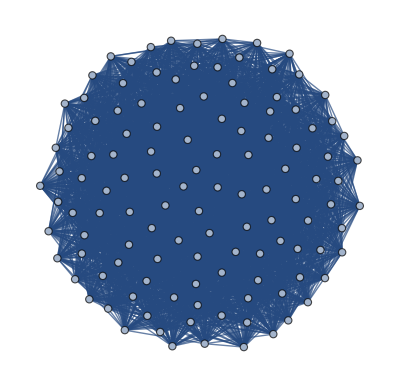

```mathematica
G=Import["/home/josera/owncloud2/clientsync/InvesEnCurso/eta/K5J9.g6"]
```

```mathematica
v=VertexCount[G]
```

120

```mathematica
VertexTransitiveGraphQ[G]
```

True

```mathematica
VertexDegree[G]
```

{51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51}

```mathematica
alpha=Length@FindIndependentVertexSet[G][[1]]
```

8

```mathematica
omega=Length@FindIndependentVertexSet[GraphComplement[G]][[1]]
```

4

```mathematica
eta=2*alpha/(alpha+(v/omega))
```

8/19

```mathematica
N[%]
```

0.421053